# Comparison of TES and OSTES on TASI data

## Definition of constants and functions

### Planck constant - J s

```mathematica
h=6.62606957 10^-34
```

6.62607×10^-34

### Speed of light - m/s

```mathematica
c=299792458
```

299792458

### Boltzmann constant - J/K

```mathematica
k=1.3806488 10^-23
```

1.38065×10^-23

### Pre - computation of hc

```mathematica
hc=h c
```

1.98645×10^-25

### Stefan-Boltzmann constant

```mathematica
σ=5.670373 10^-8
```

5.67037×10^-8

### Constant of proportionality

```mathematica
bWien=2.8977721×10^(−3)
```

0.00289777

### General constants substitution

```mathematica
a=2 h c^2
```

1.19104×10^-16

```mathematica
b=h c /k
```

0.0143878

## TASI band parameters and functions

```mathematica
BandCenters={8054.750,8164.250,8273.750,8383.250,8492.750,8602.250,8711.750,8821.250,8930.750,9040.250,9149.750,9259.250,9368.750,9478.250,9587.750,9697.250,9806.750,9916.250,10025.750,10135.250,10244.750,10354.250,10463.750,10573.250,10682.750,10792.250,10901.750,11011.250,11120.750,11230.250,11339.750,11449.250}10^-9;
```

### Response functions

```mathematica
TASIBandCenters={8054.750,8164.250,8273.750,8383.250,8492.750,8602.250,8711.750,8821.250,8930.750,9040.250,9149.750,9259.250,9368.750,9478.250,9587.750,9697.250,9806.750,9916.250,10025.750,10135.250,10244.750,10354.250,10463.750,10573.250,10682.750,10792.250,10901.750,11011.250,11120.750,11230.250,11339.750,11449.250} 10^-9;
```

```mathematica
TASIFWHM=109.5 10^-9;
```

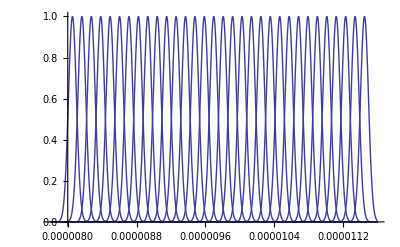

```mathematica
Show[Table[Plot[Exp[-(x-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{x,7.8 10^-6,11.6 10^-6},PlotRange->All],{i,1,Length[TASIBandCenters]}]]
```

```mathematica
TASIResponseFunction[bandn_,x_]:=Table[Exp[-(x-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{i,1,Length[TASIBandCenters]}][[bandn]]
```

## Planck’s functions

### Basic functions

#### Wien’s displacement law

```mathematica
WienLawFunction[T_]:=bWien/T
```

#### Planck’s law

```mathematica
PlanckLawFunction[T_,λ_]:=(a)/(λ^5(Exp[b / (λ T)]-1))
```

#### Inverse Planck’s law

```mathematica
InversePlanckLawFunction[R_,λ_,emis_]:=(b)/(λ Log[(a emis)/(λ^5 R)+1])
```

## Data loading

### Airborne

#### OSTES

```mathematica
OSTESAsphaltBegheli=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_asphalt_begheli_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
OSTESAsphaltHotelParking=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_asphalt_hotel_parking_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
OSTESAsphaltRooftopC=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_asphalt_rooftop_C_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
OSTESCalibrationPanels=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_calibration_panels_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
OSTESConcreteBlocks=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_concrete_blocks_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
OSTESPlasticRooftopC=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_plastic_rooftop_C_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
OSTESRubberRooftopA=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_rubber_rooftop_A_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
OSTESSvratka=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_svratka_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
OSTESVegetation=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\OSTES_vegetation_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
```

#### TES

```mathematica
TESAsphaltBegheli=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_asphalt_begheli_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
TESAsphaltHotelParking=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_asphalt_hotel_parking_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
TESAsphaltRooftopC=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_asphalt_rooftop_C_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
TESCalibrationPanels=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_calibration_panels_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
TESConcreteBlocks=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_concrete_blocks_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
TESPlasticRooftopC=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_plastic_rooftop_C_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
TESRubberRooftopA=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_rubber_rooftop_A_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
TESSvratka=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_svratka_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
TESVegetation=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\airborne\\TES_vegetation_results.txt","Data",FieldSeparators->"  "][[;;,8;;]];
```

### Ground truth

```mathematica
AsphaltBegheli=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\asphalt - begheli - mean-emissivity-ENVI_band-number.txt","Data"][[;;,2]];
AsphaltHotelParking=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\asphalt - hotel parking - mean-emissivity-ENVI_band-number.txt","Data"][[;;,2]];
AsphaltRooftopC=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\asphalt - rooftop - mean-emissivity-ENVI_band-number.txt","Data"][[;;,2]];
ConcreteBlocks=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\concrete blocks - mean-emissivity-ENVI_band-number.txt","Data"][[;;,2]];
PlasticRooftopC=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\plastic - rooftop - mean-emissivity-ENVI_band-number.txt","Data"][[;;,2]];
CalibrationPanels=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\plate - mean-emissivity-ENVI_band-number.txt","Data"][[;;,2]];
RubberRooftopA=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\rubber - mean-emissivity-ENVI_band-number.txt","Data"][[;;,2]];
```

```mathematica
Deciduous=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\ASL_reflection_deciduous.txt","Data"];
Deciduous[[;;,1]]=Deciduous[[;;,1]]10^-6;
Deciduous[[;;,2]]=1-Deciduous[[;;,2]]/100;
Deciduous=Table[NIntegrate[Interpolation[Table[{Deciduous[[k,1]],Deciduous[[k,2]]},{k,1,Length[Deciduous]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}],{j,1,Length[TASIBandCenters]}];
Deciduous=Deciduous[[6;;27]];
```

```mathematica
Water=Import["D:\\_tmp\\OSTES Matlab implementation\\results\\ground truth\\ASL_reflection_deciduous.txt","Data"];
Water[[;;,1]]=Water[[;;,1]]10^-6;
Water[[;;,2]]=1-Water[[;;,2]]/100;
Water=Table[NIntegrate[Interpolation[Table[{Water[[k,1]],Water[[k,2]]},{k,1,Length[Water]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}],{j,1,Length[TASIBandCenters]}];
Water=Water[[6;;27]];
```

## Processing

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
errorFunc2[barWidth_(*,thickness_*)][coords_,errs_]:=Return[{
Thickness[0.0005],
Line[{{coords[[1]],coords[[2]]-errs[[2,1]]},{coords[[1]],coords[[2]]+errs[[2,1]]}}],
Line[{{coords[[1]]-barWidth,coords[[2]]-errs[[2,1]]},{coords[[1]]+barWidth,coords[[2]]-errs[[2,1]]}}],
Line[{{coords[[1]]-barWidth,coords[[2]]+errs[[2,1]]},{coords[[1]]+barWidth,coords[[2]]+errs[[2,1]]}}]
}];
```

```mathematica
font="Cambria";
fontSize=22;
TASIColor=RGBColor[0,0.917,0.576];
ASTERColor=RGBColor[1,(*0,0*)0.51,0.196];
AHSColor=RGBColor[0,0.635,0.91];
approxFun[par1_,par2_,var_]:=1/(par1 var^3+par2);
lineThickness=0.005;
```

```mathematica
minOfAllSpectra=0.755507;
maxOfAllSpectra=0.988987;
```

### Asphalt Begheli

```mathematica
MeanOSTESAsphaltBegheli=Mean[OSTESAsphaltBegheli];
StdOSTESAsphaltBegheli=StandardDeviation[OSTESAsphaltBegheli];
```

```mathematica
MeanTESAsphaltBegheli=Mean[TESAsphaltBegheli];
StdTESAsphaltBegheli=StandardDeviation[TESAsphaltBegheli];
```

```mathematica
ErrorBarOSTESAsphaltBegheli=Table[{{i+0.1,MeanOSTESAsphaltBegheli[[i]]},ErrorBar[StdOSTESAsphaltBegheli[[i]]]},{i,1,22}];
ErrorBarTESAsphaltBegheli=Table[{{i-0.1,MeanTESAsphaltBegheli[[i]]},ErrorBar[StdTESAsphaltBegheli[[i]]]},{i,1,22}];
```

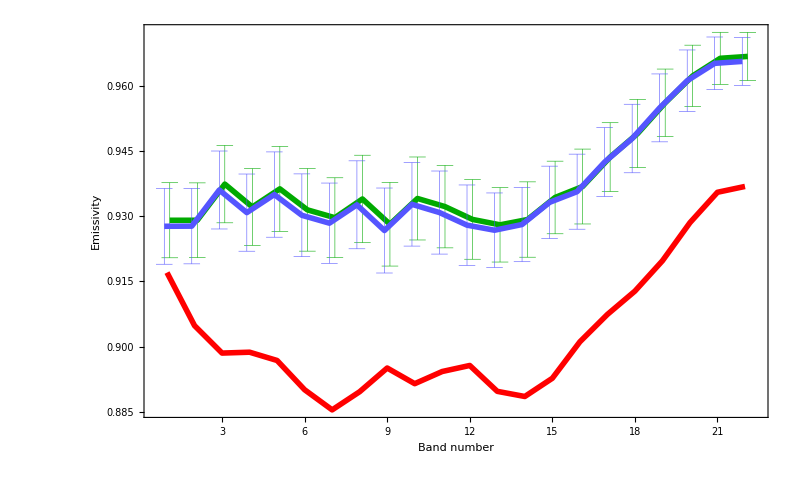
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESAsphaltBegheli,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESAsphaltBegheli,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[AsphaltBegheli,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Asphalt Begheli"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

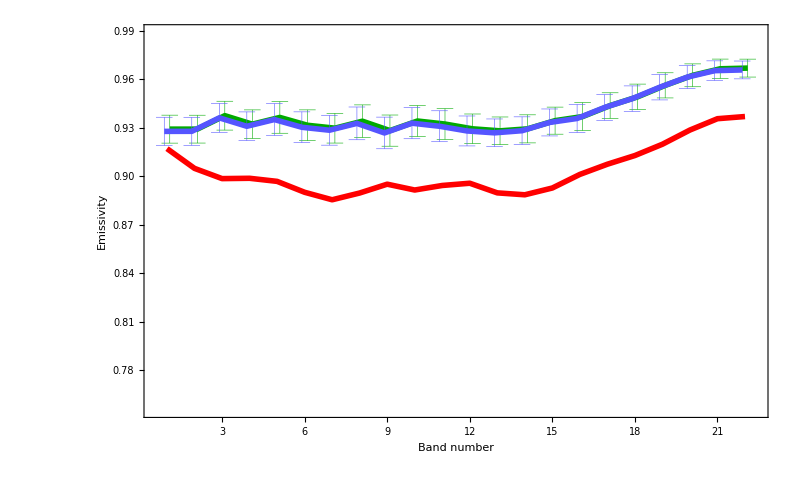
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESAsphaltBegheli,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESAsphaltBegheli,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[AsphaltBegheli,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Asphalt Begheli"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Asphalt Hotel Parking

```mathematica
MeanOSTESAsphaltHotelParking=Mean[OSTESAsphaltHotelParking];
StdOSTESAsphaltHotelParking=StandardDeviation[OSTESAsphaltHotelParking];
```

```mathematica
MeanTESAsphaltHotelParking=Mean[TESAsphaltHotelParking];
StdTESAsphaltHotelParking=StandardDeviation[TESAsphaltHotelParking];
```

```mathematica
ErrorBarOSTESAsphaltHotelParking=Table[{{i+0.1,MeanOSTESAsphaltHotelParking[[i]]},ErrorBar[StdOSTESAsphaltHotelParking[[i]]]},{i,1,22}];
ErrorBarTESAsphaltHotelParking=Table[{{i-0.1,MeanTESAsphaltHotelParking[[i]]},ErrorBar[StdTESAsphaltHotelParking[[i]]]},{i,1,22}];
```

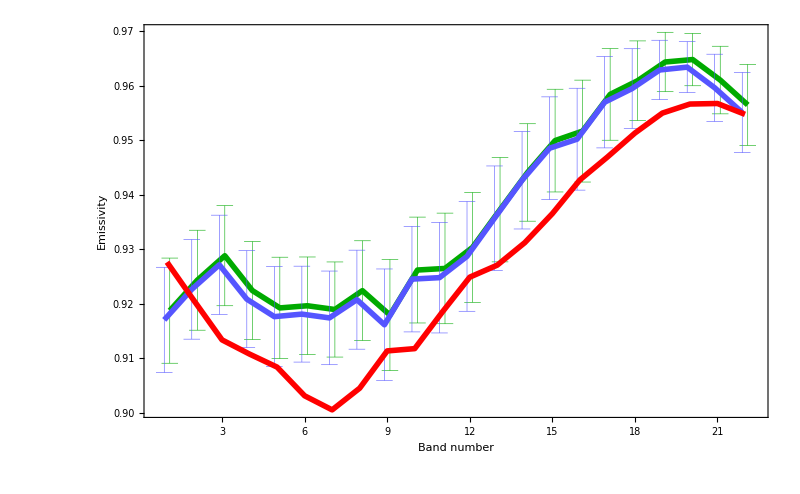
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESAsphaltHotelParking,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESAsphaltHotelParking,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[AsphaltHotelParking,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Asphalt Hotel Parking"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

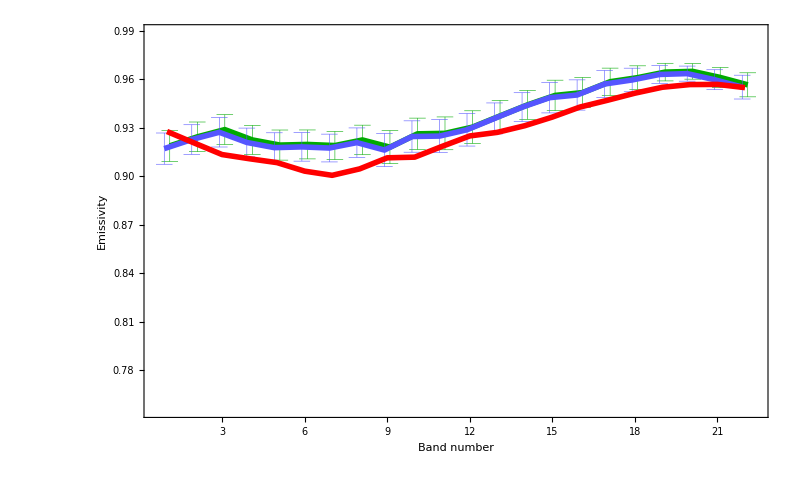
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESAsphaltHotelParking,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESAsphaltHotelParking,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[AsphaltHotelParking,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Asphalt Hotel Parking"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Asphalt Rooftop C

```mathematica
MeanOSTESAsphaltRooftopC=Mean[OSTESAsphaltRooftopC];
StdOSTESAsphaltRooftopC=StandardDeviation[OSTESAsphaltRooftopC];
```

```mathematica
MeanTESAsphaltRooftopC=Mean[TESAsphaltRooftopC];
StdTESAsphaltRooftopC=StandardDeviation[TESAsphaltRooftopC];
```

```mathematica
ErrorBarOSTESAsphaltRooftopC=Table[{{i+0.1,MeanOSTESAsphaltRooftopC[[i]]},ErrorBar[StdOSTESAsphaltRooftopC[[i]]]},{i,1,22}];
ErrorBarTESAsphaltRooftopC=Table[{{i-0.1,MeanTESAsphaltRooftopC[[i]]},ErrorBar[StdTESAsphaltRooftopC[[i]]]},{i,1,22}];
```

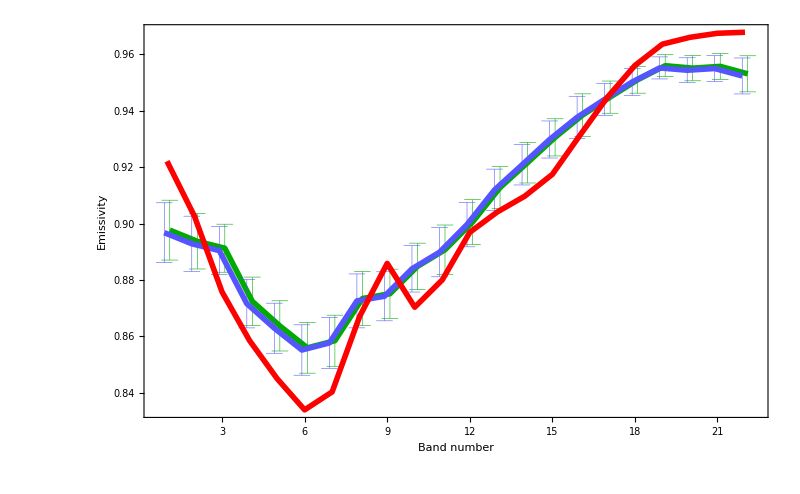
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESAsphaltRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESAsphaltRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[AsphaltRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Asphalt Rooftop C"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

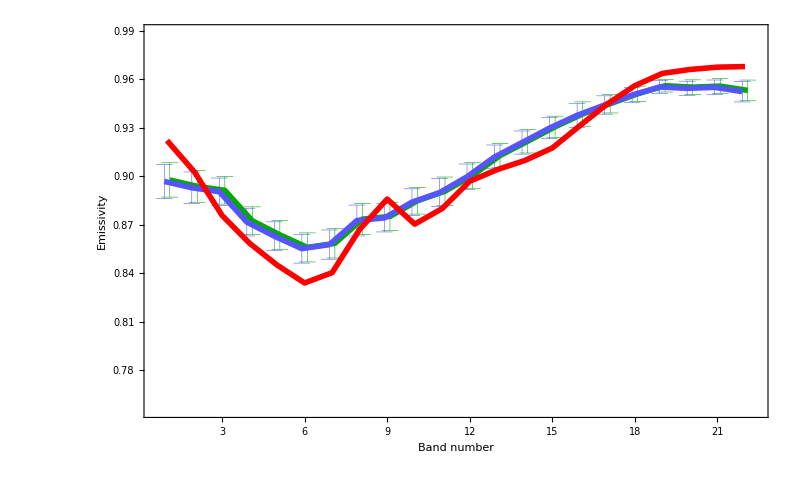
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESAsphaltRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESAsphaltRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[AsphaltRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Asphalt Rooftop C"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Calibration Panels

```mathematica
MeanOSTESCalibrationPanels=Mean[OSTESCalibrationPanels];
StdOSTESCalibrationPanels=StandardDeviation[OSTESCalibrationPanels];
```

```mathematica
MeanTESCalibrationPanels=Mean[TESCalibrationPanels];
StdTESCalibrationPanels=StandardDeviation[TESCalibrationPanels];
```

```mathematica
ErrorBarOSTESCalibrationPanels=Table[{{i+0.1,MeanOSTESCalibrationPanels[[i]]},ErrorBar[StdOSTESCalibrationPanels[[i]]]},{i,1,22}];
ErrorBarTESCalibrationPanels=Table[{{i-0.1,MeanTESCalibrationPanels[[i]]},ErrorBar[StdTESCalibrationPanels[[i]]]},{i,1,22}];
```

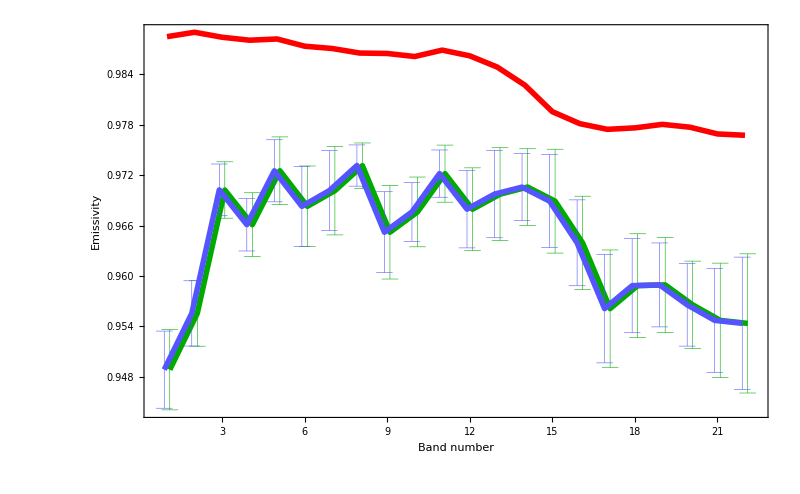
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESCalibrationPanels,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESCalibrationPanels,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[CalibrationPanels,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Calibration Panels"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

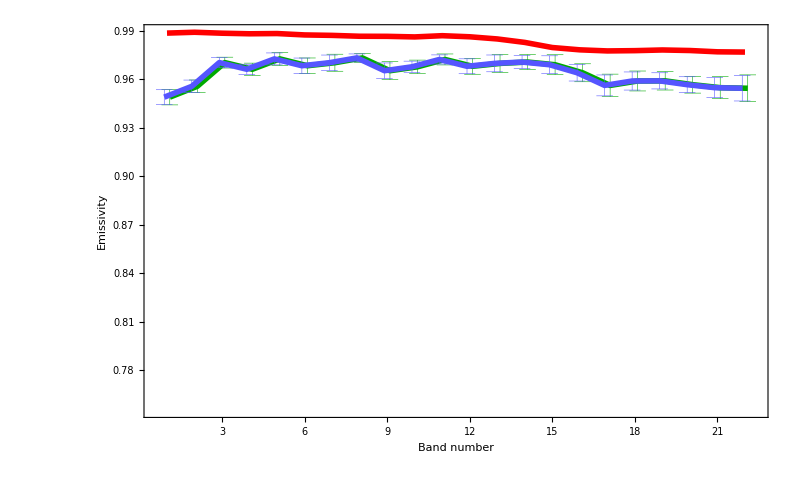
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESCalibrationPanels,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESCalibrationPanels,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[CalibrationPanels,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Calibration Panels"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Concrete Blocks

```mathematica
MeanOSTESConcreteBlocks=Mean[OSTESConcreteBlocks];
StdOSTESConcreteBlocks=StandardDeviation[OSTESConcreteBlocks];
```

```mathematica
MeanTESConcreteBlocks=Mean[TESConcreteBlocks];
StdTESConcreteBlocks=StandardDeviation[TESConcreteBlocks];
```

```mathematica
ErrorBarOSTESConcreteBlocks=Table[{{i+0.1,MeanOSTESConcreteBlocks[[i]]},ErrorBar[StdOSTESConcreteBlocks[[i]]]},{i,1,22}];
ErrorBarTESConcreteBlocks=Table[{{i-0.1,MeanTESConcreteBlocks[[i]]},ErrorBar[StdTESConcreteBlocks[[i]]]},{i,1,22}];
```

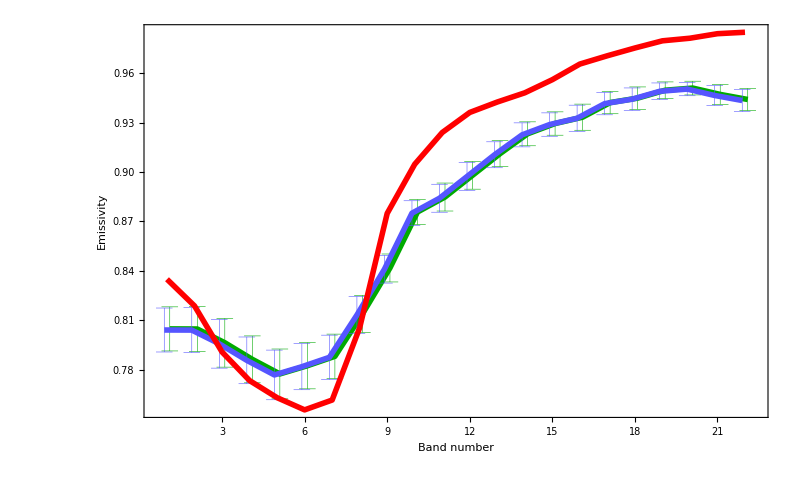
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESConcreteBlocks,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESConcreteBlocks,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[ConcreteBlocks,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Concrete Blocks"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

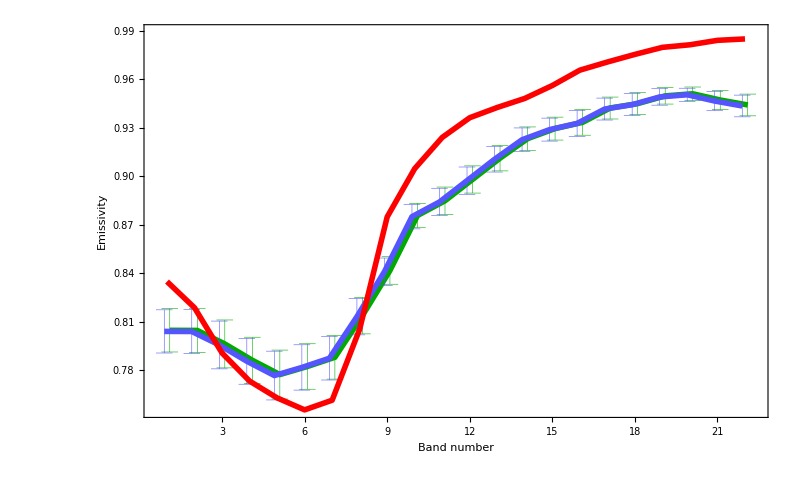
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESConcreteBlocks,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESConcreteBlocks,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[ConcreteBlocks,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Concrete Blocks"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Plastic Rooftop C

```mathematica
MeanOSTESPlasticRooftopC=Mean[OSTESPlasticRooftopC];
StdOSTESPlasticRooftopC=StandardDeviation[OSTESPlasticRooftopC];
```

```mathematica
MeanTESPlasticRooftopC=Mean[TESPlasticRooftopC];
StdTESPlasticRooftopC=StandardDeviation[TESPlasticRooftopC];
```

```mathematica
ErrorBarOSTESPlasticRooftopC=Table[{{i+0.1,MeanOSTESPlasticRooftopC[[i]]},ErrorBar[StdOSTESPlasticRooftopC[[i]]]},{i,1,22}];
ErrorBarTESPlasticRooftopC=Table[{{i-0.1,MeanTESPlasticRooftopC[[i]]},ErrorBar[StdTESPlasticRooftopC[[i]]]},{i,1,22}];
```

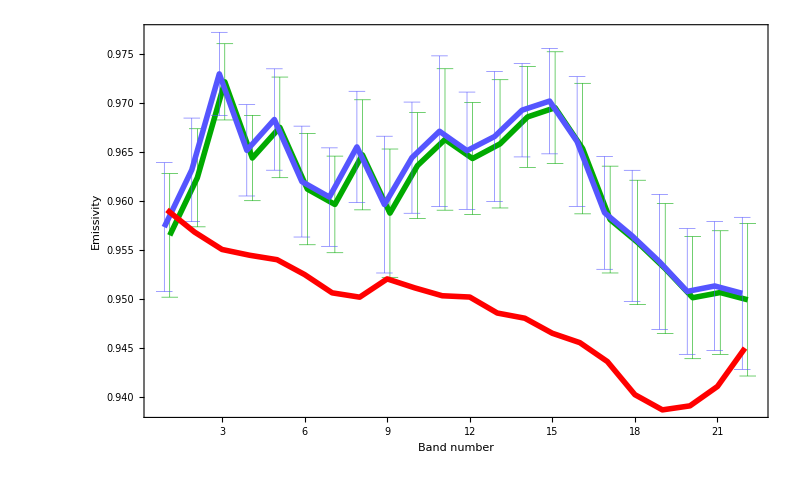
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESPlasticRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESPlasticRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[PlasticRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Plastic Rooftop C"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

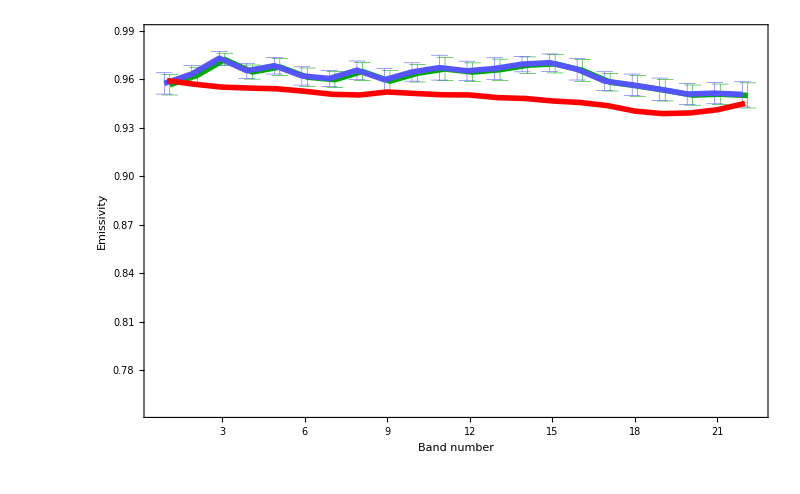
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESPlasticRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESPlasticRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[PlasticRooftopC,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Plastic Rooftop C"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Rubber Rooftop A

```mathematica
MeanOSTESRubberRooftopA=Mean[OSTESRubberRooftopA];
StdOSTESRubberRooftopA=StandardDeviation[OSTESRubberRooftopA];
```

```mathematica
MeanTESRubberRooftopA=Mean[TESRubberRooftopA];
StdTESRubberRooftopA=StandardDeviation[TESRubberRooftopA];
```

```mathematica
ErrorBarOSTESRubberRooftopA=Table[{{i+0.1,MeanOSTESRubberRooftopA[[i]]},ErrorBar[StdOSTESRubberRooftopA[[i]]]},{i,1,22}];
ErrorBarTESRubberRooftopA=Table[{{i-0.1,MeanTESRubberRooftopA[[i]]},ErrorBar[StdTESRubberRooftopA[[i]]]},{i,1,22}];
```

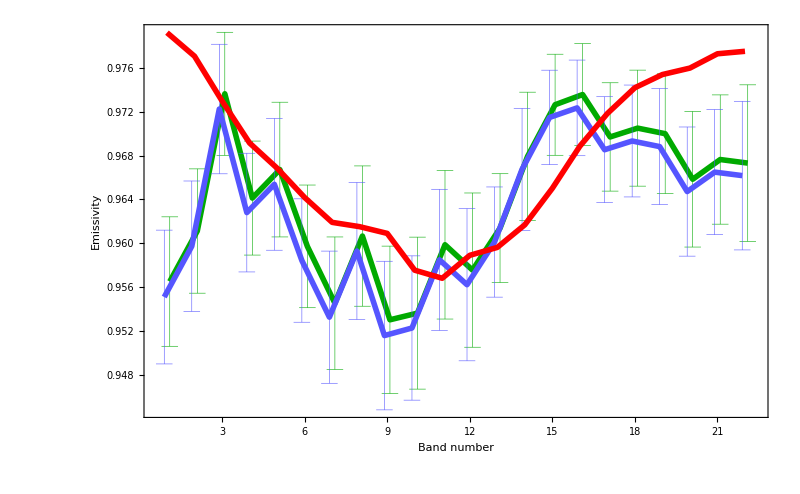
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESRubberRooftopA,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESRubberRooftopA,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[RubberRooftopA,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Rubber Rooftop A"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

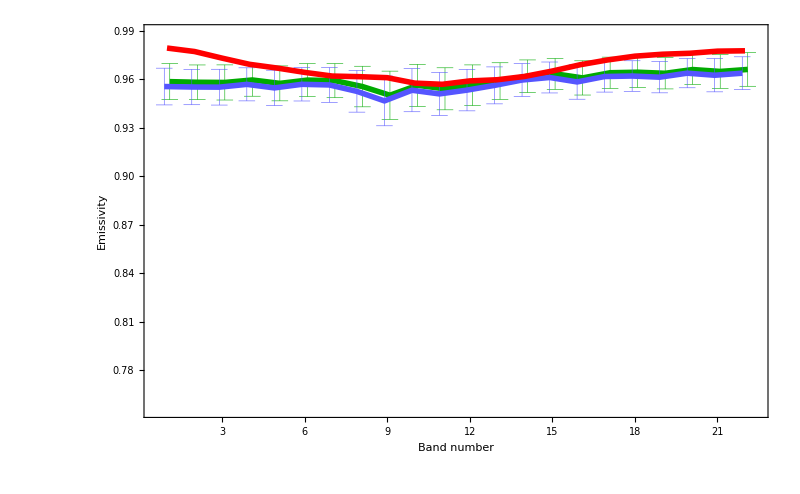
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESRubberRooftopA,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESRubberRooftopA,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[RubberRooftopA,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Rubber Rooftop A"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Svratka

```mathematica
MeanOSTESSvratka=Mean[OSTESSvratka];
StdOSTESSvratka=StandardDeviation[OSTESSvratka];
```

```mathematica
MeanTESSvratka=Mean[TESSvratka];
StdTESSvratka=StandardDeviation[TESSvratka];
```

```mathematica
ErrorBarOSTESSvratka=Table[{{i+0.1,MeanOSTESSvratka[[i]]},ErrorBar[StdOSTESSvratka[[i]]]},{i,1,22}];
ErrorBarTESSvratka=Table[{{i-0.1,MeanTESSvratka[[i]]},ErrorBar[StdTESSvratka[[i]]]},{i,1,22}];
```

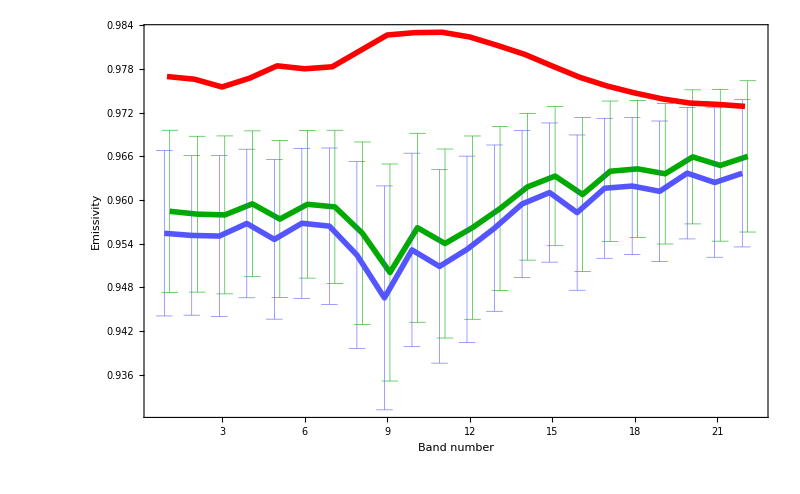
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESSvratka,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESSvratka,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[Water,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Svratka"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

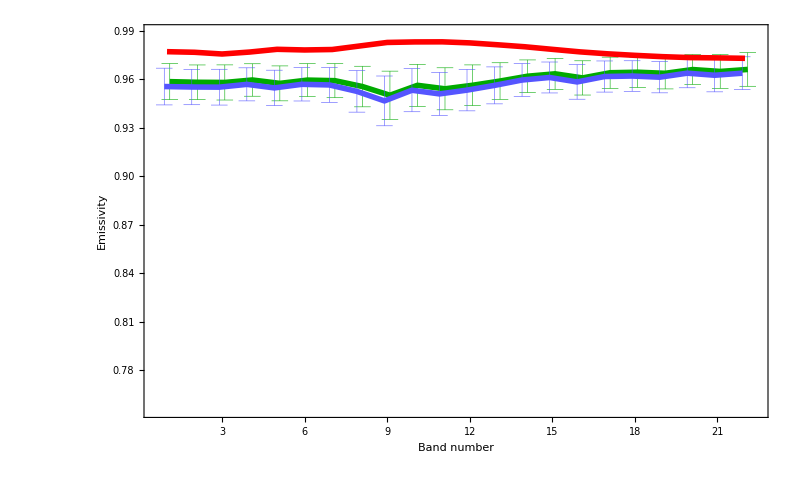
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESSvratka,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESSvratka,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[Water,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Svratka"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Vegetation

```mathematica
MeanOSTESVegetation=Mean[OSTESVegetation];
StdOSTESVegetation=StandardDeviation[OSTESVegetation];
```

```mathematica
MeanTESVegetation=Mean[TESVegetation];
StdTESVegetation=StandardDeviation[TESVegetation];
```

```mathematica
ErrorBarOSTESVegetation=Table[{{i+0.1,MeanOSTESVegetation[[i]]},ErrorBar[StdOSTESVegetation[[i]]]},{i,1,22}];
ErrorBarTESVegetation=Table[{{i-0.1,MeanTESVegetation[[i]]},ErrorBar[StdTESVegetation[[i]]]},{i,1,22}];
```

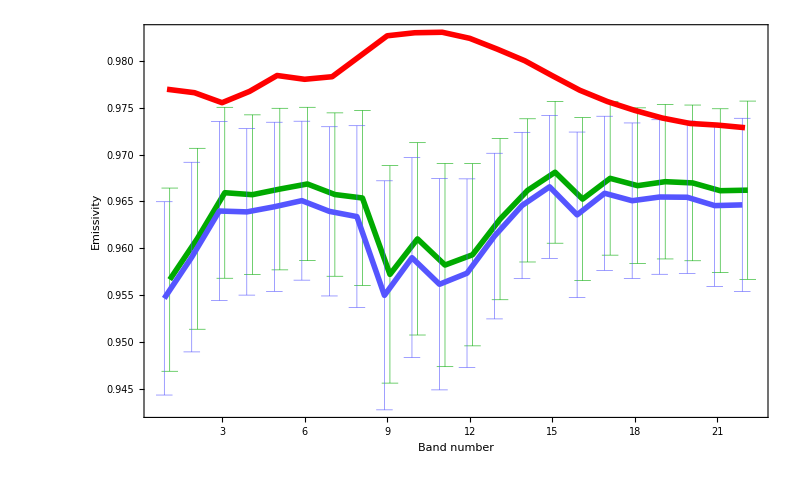
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESVegetation,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESVegetation,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[Deciduous,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->All,
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Vegetation"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

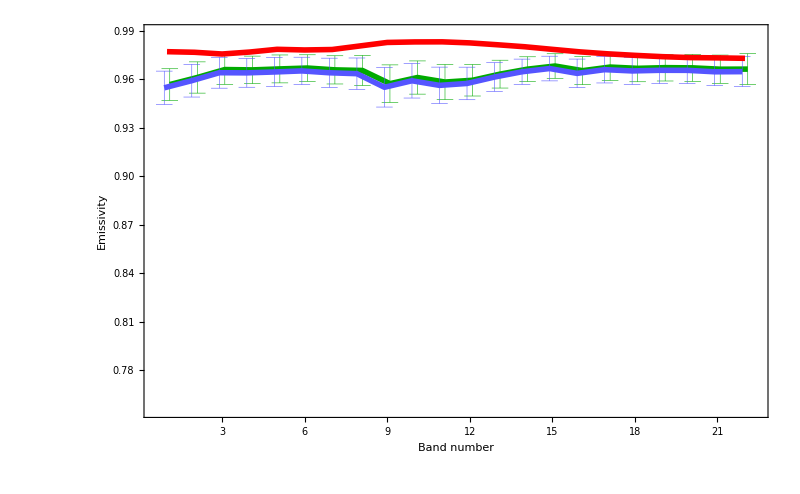
-Graphics- |

```mathematica
TableForm[{
{Show[
ErrorListPlot[ErrorBarOSTESVegetation,Joined->True,PlotStyle->{Thickness[lineThickness],Darker[Green]},ErrorBarFunction->errorFunc2[0.3]],
ErrorListPlot[ErrorBarTESVegetation,Joined->True,PlotStyle->{Thickness[lineThickness],Lighter[Blue]},ErrorBarFunction->errorFunc2[0.3]],
ListPlot[Deciduous,Joined->True,PlotStyle->{Thickness[lineThickness],Red}],
PlotRange->{minOfAllSpectra,maxOfAllSpectra},
ImageSize->800,
Frame->True,
Axes->{False,False},
FrameLabel->{{"Emissivity",None},{"Band number","Vegetation"}},
LabelStyle->{FontSize->22,FontFamily->font}
],
LineLegend[{Darker[Green],Lighter[Blue],Red},{"OSTES","TES","FTIR"},LabelStyle->{FontSize->18,FontFamily->font}]}
}]
```

### Computing MAX and MIN of all spectra

```mathematica
minOfAllSpectra=Min[{
MeanOSTESVegetation,MeanTESVegetation,
MeanOSTESSvratka,MeanTESSvratka,
MeanOSTESRubberRooftopA,MeanTESRubberRooftopA,
MeanOSTESPlasticRooftopC,MeanTESPlasticRooftopC,
MeanOSTESConcreteBlocks,MeanTESConcreteBlocks,
MeanOSTESCalibrationPanels,MeanTESCalibrationPanels,
MeanOSTESAsphaltRooftopC,MeanTESAsphaltRooftopC,
MeanOSTESAsphaltHotelParking,MeanTESAsphaltHotelParking,
MeanOSTESAsphaltBegheli,MeanTESAsphaltBegheli,
AsphaltBegheli,
AsphaltHotelParking,
AsphaltRooftopC,
ConcreteBlocks,
PlasticRooftopC,
CalibrationPanels,
RubberRooftopA,
Deciduous,
Water
}];
```

```mathematica
maxOfAllSpectra=Max[{
MeanOSTESVegetation,MeanTESVegetation,
MeanOSTESSvratka,MeanTESSvratka,
MeanOSTESRubberRooftopA,MeanTESRubberRooftopA,
MeanOSTESPlasticRooftopC,MeanTESPlasticRooftopC,
MeanOSTESConcreteBlocks,MeanTESConcreteBlocks,
MeanOSTESCalibrationPanels,MeanTESCalibrationPanels,
MeanOSTESAsphaltRooftopC,MeanTESAsphaltRooftopC,
MeanOSTESAsphaltHotelParking,MeanTESAsphaltHotelParking,
MeanOSTESAsphaltBegheli,MeanTESAsphaltBegheli,
AsphaltBegheli,
AsphaltHotelParking,
AsphaltRooftopC,
ConcreteBlocks,
PlasticRooftopC,
CalibrationPanels,
RubberRooftopA,
Deciduous,
Water
}];
```